# Machine Learning

## Etienne Bernard, Wolfram Research

## Machine Learning ?

### Computer “learns” a model from data

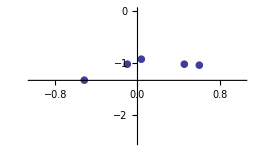
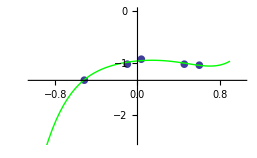
-Graphics-	⟶	-Graphics-

{ →cat, →dog,...}	⟶	-Graphics-

### Typical tasks

Classification of images, sound, text, etc.

→cat, →dog,...

Prediction of a variable in a dataset

(6 yo, female) → 1.15 m, (11 yo, male) → 1.48 m, ...

Prediction of a time series

Text translation

“the house is blue” → “la maison est bleue”

Anomaly detection

-Graphics-

Data clustering

-Graphics-

Robot learning how to move

## In the Wolfram Language

### High-level functionalities

Predict, Classify, ClusterClassify, FeatureExtraction, etc.

Task oriented

Automatic

Wide range of data types (Numerical, Images, text, etc.)

### Low-level functionalities

Neural network framework (NetTrain, NetChain, etc.)

Model oriented

High flexibility

See talk of Sebastian Bodenstein  - Friday 10 AM

### Developed using Machine Learning

Built-in classifiers, ImageIdentify, TextCases, etc.

## High-level functions

### Supervised Learning

Classify

Predict

FindFormula

### Unsupervised Learning

DimensionReduction

FeatureExtraction

ClusterClassify

ClusteringTree

FindDistribution

### “Active” Learning

BayesianMinimization

11.1:

ActiveClassification

ActivePrediction

## Classify & Predict

### Predict - basic example

```mathematica
data={-1.2->1.2,1.4->1.4,3.1->1.8,4.5->1.6};
```

```mathematica
Show[Plot[{
p[x],
p[x]+StandardDeviation[p[x,"Distribution"]],p[x]-StandardDeviation[p[x,"Distribution"]]
},{x,-2,6},PlotStyle->{Blue,Gray,Gray},Filling->{2->{3}},Exclusions-> False,PerformanceGoal->"Speed",PlotLegends->{"Prediction","Confidence Interval"}],ListPlot[List@@@data,PlotStyle->Red,PlotLegends->{"Data"}]]
```

### Image Classification

```mathematica
ServiceConnect["BingSearch"]
```

ServiceObject[…]

```mathematica
creaturesname={"centaur","griffin","dragon","unicorn"};
```

```mathematica
creatureimages=ServiceExecute["BingSearch","Search",{"Query"->#,"SearchType"->"Images","MaxItems"->60,"Elements"->"Thumbnails"}] & /@ creaturesname;
```

```mathematica
labeledcreatures=RandomSample[DeleteDuplicates[Flatten[Thread /@ Thread[creatureimages->creaturesname]]]];
```

```mathematica
training = labeledcreatures[[;;100]];
test = labeledcreatures[[101;;]];
```

## FeatureExtraction

Learn a feature extractor from data

Use “built-in” feature extractor + dimensionality reduction

Useful for most machine learning application

```mathematica
mythicalcreatures=labeledcreatures[[All,1]];
```

### Visualization

```mathematica
features=FeatureExtract[mythicalcreatures];
```

```mathematica
xy=DimensionReduce[features,2];
```

```mathematica
ListPlot[List/@xy,PlotMarkers->(Image[#,ImageSize->30]& /@ mythicalcreatures),ImageSize->1000]
```

### Search system

```mathematica
dataset=mythicalcreatures[[;;150]];
queries=mythicalcreatures[[151;;]];
```

```mathematica
fe=FeatureExtraction[dataset]
```

```mathematica
nf=Nearest[fe[dataset]->Automatic]
```

```mathematica
nearestcreature=dataset[[First@nf[fe[#]]]]&
```

## Built-in Machine Learning

### Built-in Classifiers

```mathematica
Classify["Language","Quelle est cette langue"]
```

```mathematica
Classify["FacebookTopic","I play guitar"]
```

```mathematica
Classify["NotablePerson",-Graphics-]
```

### ImageIdentify

```mathematica
ImageIdentify[-Graphics-]
```

```mathematica
ImageIdentify[-Graphics-]
```

### TextStructure

```mathematica
str=TextStructure["The house is blue. My dog is fast."]
```

### TextCases

```mathematica
moon=WikipediaData["Moon"];
```

Sentences, words, ...

```mathematica
TextCases[moon,"Sentence"]
```

Grammatical units:

```mathematica
TextCases[moon,"Noun"]
```

Languages

```mathematica
TextCases["John and Mary went to Italy. Et je suis francais. La casa es azul. And english again", "English"]
```

```mathematica
TextCases["John and Mary went to Italy. Et je suis francais. La casa es azul. And english again", {"English","Spanish"}->{"Type","Position"}]
```

Various entity types:

```mathematica
TextCases[moon,"Country"]
```

Quantities:

```mathematica
TextCases[moon,"Quantity"->"Interpretation"]
```

Also:

“PhoneNumber”

“EmailAddress”

“URL”

...

## What’s next

Multiple-output prediction

LearnDistribution

MissingImputation

AnomalyDetection

...

Reinforcement learning

??